```mathematica
sol=DSolve[{x'[t]==4x[t]-y[t]+Exp[3t](t+Sin[t]), y'[t]==x[t]+2y[t]+t Exp[3t]Cos[t],x[0]==2,y[0]==0},{x[t],y[t]},t]
```

{{x[t]→1/6 ⅇ^(3 t) (18+24 t+3 t^2+t^3-6 Cos[t]+6 t Cos[t]-18 Sin[t]),y[t]→1/6 ⅇ^(3 t) (-6+24 t+t^3+6 Cos[t]+6 t Cos[t]-18 Sin[t]+6 t Sin[t])}}

```mathematica
fun = Table[sol[[1]][[i]][[2]],{i,1,Length[sol[[1]]]}];
```

```mathematica
euler=ReadList["D:\\VisualStdudio\\calculatem\\calculation-methods-labs\\lab6\\lab6\\ImplicitEuler.txt",Number,RecordLists->True];
```

```mathematica
adams=ReadList["D:\\VisualStdudio\\calculatem\\calculation-methods-labs\\lab6\\lab6\\AdamsBashford.txt",Number,RecordLists->True];
```

```mathematica
PredictionCorection=ReadList["D:\\VisualStdudio\\calculatem\\calculation-methods-labs\\lab6\\lab6\\PredictionCorection.txt",Number,RecordLists->True];
```

```mathematica
tau = 0.1;T=1;
```

```mathematica
timetable = Table[i,{i,0,T,tau}];
```

```mathematica
n = Length[euler[[1]]];
```

```mathematica
dotseuler = Table[euler[[All,i]],{i,1,n}];
```

```mathematica
dotsadams=Table[adams[[All,i]],{i,1,n}];
```

```mathematica
dotsPredictionCorection=Table[PredictionCorection[[All,i]],{i,1,n}];
```

```mathematica
pointseuler  = Table[Table[{timetable[[j]],dotseuler [[i]][[j]]},{j,1,Length[timetable]}],{i,1,n}];
```

```mathematica
pointsadams  = Table[Table[{timetable[[j]],dotsadams [[i]][[j]]},{j,1,Length[timetable]}],{i,1,n}];
```

```mathematica
pointsPredictionCorection  = Table[Table[{timetable[[j]],dotsPredictionCorection [[i]][[j]]},{j,1,Length[timetable]}],{i,1,n}];
```

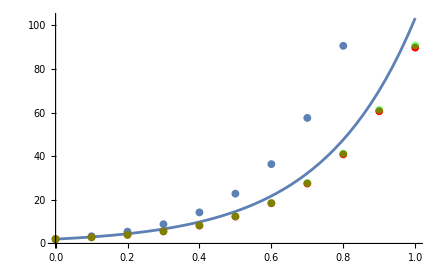
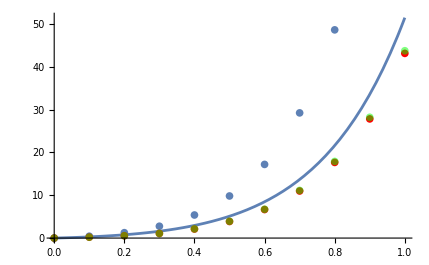

```mathematica
Paints = Table[Show[Plot[fun[[i]],{t,0,T}], ListPlot[pointseuler[[i]]], ListPlot[pointsadams[[i]], PlotStyle->Red], ListPlot[pointsPredictionCorection[[i]], PlotStyle->{Green, Opacity[0.5]}]],{i,1,n}]
```